# A simple classical density functional theory code for ideal fluids

We will write a simple Mathematica version 9 or superior code to study an ideal fluid by classical density functional theory.
Our objective is to compute the radial distribution function of such a fluid.
Our problem, as presented here, will be treated in one dimension, i.e., as a purely radial problem.

```mathematica
(* In the Mathematica language, comments should be put between these symbols *)
```

## Definitions

First, we discretize the one-dimensional space into a given number of points. This number is:

```mathematica
pts=1000; (* 100 is a good starting point *)
```

What will you consider far enough of the solute to have a radial distribution function constant equal to 1?
For instance, in water, the radial distribution function is constant and 1 after 15 Angstroms.

```mathematica
gridmax=15; (* in angstroms, 15 is a good starting point *)
```

The distance in angstroms between two grid nodes is given by

```mathematica
dx=gridmax/(pts-1);
```

Then, variable grid will contain all the positions of grid points, from 0 to gridmax. It has pts values.

```mathematica
grid=Range[0,gridmax,dx];
```

Next, we define a table of variables that will contain the solvent density at each grid nodes. It thus has pts values.
We also know that these densities must be positive. A negative density is non-sense.

```mathematica
varsn=Table[Unique[n$],{pts}];
constraintOfPositiveDensity=(#1≥0&)/@varsn; (* condition ≥0 is mapped to all variables *)
```

Here come some physical quantities

```mathematica
kb=1.38065*10^-26(* Boltzmann constant in kJ/K *);
T=300 (* Temperature in K*);
Na=6.022*10^23 (* Avogadro constant in mol^-1 *);
β=1/(Na kb T) (* Boltzmann factor in kJ/mol *);
```

We define the function d[i,j] that returns the distance between two grid nodes i and j.

```mathematica
d[i_,j_]:=d[i,j]=EuclideanDistance[grid⟦i⟧,grid⟦j⟧]; (* here we use a Mathematica trick called memoization, for "Functions That Remember Values They Have Found" *)
```

We define some Lennard-Jones interaction between two nodes i and j. The Lennard-Jones parameters are also introduced here.

```mathematica
ϵ=1.8; (* kJ/mol *)
σ=2.7;(* Angstroms *)
v[i_,j_]:=v[i,j]=Module[{r=d[i,j]},
Piecewise[{
{100,r≤2.2},(* a maximum value limited to 100, not ∞ *)
{4 ϵ ((σ/r)^12-(σ/r)^6),2<r≤3σ},(* standard LJ potential *)
{0,r>3σ} (* standard LJ cutoff *)
}]
];
```

The Helmholtz free energy functional is, in our approximation, the sum of the ideal functional and external functional

```mathematica
ftot:=fid+fext
```

where the ideal part of the functional is given by

```mathematica
fid=β^-1 *dx*varsn.(Log[varsn]-1);
```

and the external part by

```mathematica
vext=Table[v[i,1],{i,1,Length[varsn]}]/.Indeterminate->(vext//Max);
fext=vext.varsn dx;
(*ftot:=fid+fext;*)
```

## Minimization of the functional

```mathematica
min=FindMinimum[
{ftot,constraintOfPositiveDensity},(* this minimizes ftot given the constraints on the density above *)
Table[{varsn[[i]],1},{i,1,Length[varsn]}]
]; (* note that Mathematica may print you warnings with respect to its convergence criteria or so *)
mindata=Transpose[{grid,varsn/.Last[min]}];
```

## Comparison to experimental results for neon and plotting

The following points, called “data” correspond to the radial distribution function extracted from the experimental measurements by Graaf and Mozer in Structure Study of Liquid Neon by Neutron Diffraction, J. Chem. Phys. 55, 4967 (1971).

```mathematica
dataexp={{0.,0.},{0.5,0.},{1.,0},{1.5,0.},{2.,0},{2.5,0.07},{2.5868263,0.34471543},{2.6586826,0.54526742},{2.6946108,0.73170423},{2.7664671,1.0705326},{2.8023952,1.2526983},{2.8383234,1.3636697},{2.8742515,1.6315461},{2.9461078,1.8636202},{3.0179641,2.0220238},{3.0898204,2.1031591},{3.1976048,1.95629},{3.2694611,1.7949447},{3.3413174,1.632459},{3.4491018,1.4718714},{3.5209581,1.3396045},{3.6287425,1.2105453},{3.7005988,1.1116598},{3.8083832,1.0022286},{3.9520958,0.89293012},{4.1317365,0.79967027},{4.4550898,0.74771432},{4.7784431,0.79883772},{4.994012,0.86708395},{5.1377246,0.93392205},{5.2814371,0.99712271},{5.497006,1.0709936},{5.6766467,1.1258889},{5.8562874,1.1543664},{5.9640719,1.156144},{6.2155689,1.1151688},{6.4670659,1.0523328},{6.6467066,0.99817584},{6.8622754,0.94715922},{7.2934132,0.92080272},{7.5808383,0.94881979},{7.8682635,0.98508354},{8.1556886,1.0187913},{8.5149701,1.0466287},{8.8742515,1.0265786},{9.3413174,0.9964609},{9.6646707,0.97989401},{10.131737,0.97559529},{10.45509,0.98933086},{10.886228,1.0096823},{11.353293,1.0141324},{11.784431,1.0068248}};
```

We interpolate the experimental data (data) and the computed density that minimizes the functional, i.e., the equilibrium one

```mathematica
g=Interpolation[mindata,InterpolationOrder->1];
gexp=Interpolation[dataexp,InterpolationOrder->1];
```

And we plot them on top of the analytical results

General::unfl: Underflow occurred in computation.

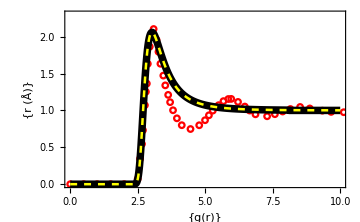

```mathematica
Show[
ListPlot[
dataexp,
PlotRange->{{0,10},{0,2.3}},
PlotMarkers->{Graphics[{Red,Circle@{0,0}}],0.05},
Frame->True,
FrameLabel->{
{"g(r)"},
{"r (Å)"}
},
BaseStyle->{Medium,FontFamily->"Times",FontSize->16}

],
Plot[{g[r],Exp[-β 4 ϵ ((σ/r)^12-(σ/r)^6)]},{r,0,10},PlotStyle->{{Thickness[0.015],Black},{Thickness[0.005],Yellow,Dashed}}]
]
(*sometimes an underflow occurs without consequence on the results*)
```

```mathematica
Plot3D[Interpolation[mindata,InterpolationOrder->10][Sqrt[x^2+y^2]],{x,-7,7},{y,-7,7},
PlotRange->{0,2.1},
PerformanceGoal->"Quality",
MaxRecursion->5,Mesh->None,
AxesLabel->{"x","y","ρ_eq/ρ_b"},
BaseStyle->{Medium,FontFamily->"Times",FontSize->12},
Ticks->{{-5,{-2.5,""},0,{2.5,""},5},{-5,{-2.5,""},0,{2.5,""},5},{0,1,2}},
PlotStyle->Opacity[0.95](*,PlotPoints->100*)(*for nice graphics but CPU demanding*)
]
```

-Graphics3D-

```mathematica
Plot3D[
gexp[Sqrt[x^2+y^2]],{x,-7,7},{y,-7,7},PlotRange->{0,2.1},
PerformanceGoal->"Quality",
MaxRecursion->5,Mesh->None,
AxesLabel->{"x","y","ρ_eq/ρ_b"},
BaseStyle->{Medium,FontFamily->"Times",FontSize->12},
Ticks->{{-5,{-2.5,""},0,{2.5,""},5},{-5,{-2.5,""},0,{2.5,""},5},{0,1,2}},
PlotStyle->Opacity[0.95](*,PlotPoints->100*)(*for nice graphics*)]
```

-Graphics3D-